# The number of achieved points at finale of Eurovision through the years (1975-2019)

For this assignment I will be analyzing the data from the Eurovision contest, to compare how well a certain country did in the finale of the contest based on points. 
First we will import the data. This data was found on Kaggle (https://www.kaggle.com/datasets/datagraver/eurovision-song-contest-scores-19752019 ). I’ve imported the data as a csv file, because it was easier to work with. I have added my own headers for the file, in accordance with the data that is useful to me. The character encoding will be UTF-8.

```mathematica
data = Import[NotebookDirectory[] <> "eurovision_song_contest_1975_2019.csv", "Table",FieldSeparators -> ",",HeaderLines ->0
, CharacterEncoding-> "UTF-8"]//Prepend[#, {"Year", "Finale", "Excess", "Jurry/Television", "From","To", "Points", "Double"}]&//ResourceFunction["DatasetWithHeaders"]
```

Dataset[<>]

Now that we have imported the data, we will filtrate what is useful. We will be able to choose a year from which onward we observe the data. The third column is not useful to us in this case. The double column shows where the “To the country” and “From the country” overlap, so we will first remove those rows, and then remove the column.

First we will filtrate the years. We will, for now, choose to look at the data from the year 2000 onward. This filtered data we will name data1.

```mathematica
data1=data // Query[Select[#Year >= 2000 &]]
```

Dataset[<>]

Now we will deal with the “Double” column issue by choosing only the columns where “From country” and “To country” don’t match. We will give the new filtered data the name data2.

```mathematica
data2 = data1//Query[Select[#From != #To  &]]
```

Dataset[<>]

Next we will get rid of the excess columns by choosing only the columns we are interested in. This filtered data we will name data3.

```mathematica
data3 = data2//Query[All, {1,2,5,6,7}]
```

Dataset[<>]

Now we have more manageable data. 
Since we are interested only in the scores in the finals, but also want to have every year represented (not just those when a country qualified for the finals) we will set the semi-final scores to 0. Now we will have a clear view of when the country did and did not qualify for the finals, and how good were its scores. We also know that if the country does not appear a certain year, it wasn’t competing. This data we will name data4.

```mathematica
data4=data3//Query[All,<|  #,"Points" -> If[#Finale != "f", 0, #Points] |>&]
```

Dataset[<>]

It is finally time to choose which country we are interested in. For this we will filter by the “To the country” column. In this case we have randomly chosen Slovenia (for no apparent reason). We will name such filtered data dataS.

```mathematica
dataS=data4// Query[Select [#To == "Slovenia" &]]
```

The only thing left to do is to sum up the points for every year. We will then get a table which is easy to show on a graph.

```mathematica
dataGraph =dataS// Query[GroupBy[{#Year}&]/* Values, <|"Year"-> Query[First, "Year"], "Points" -> Query[Total, "Points"]|>]
```

Last but not least, we have a visual representation of the country’s achievements through the years.

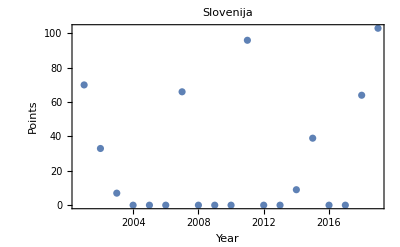

```mathematica
ListPlot[dataGraph, PlotLabel-> "Slovenija", FrameLabel->{"Year","Points"}, Frame -> {{True, False},{True, False}}]
```

Now that we know all the steps, we can make a function that will combine them all.

```mathematica
function[year_, country_]:=data//
 Query[Select[#Year >= year &]]//
Query[Select[#From != #To  &]]//
Query[All, {1,2,5,6,7}]//
Query[All,<|  #,"Points" -> If[#Finale != "f", 0, #Points] |>&]//
 Query[Select [#To == country &]]// Query[GroupBy[{#Year}&]/* Values, <|"Year"-> Query[First, "Year"], "Points" -> Query[Total, "Points"]|>]
```

```mathematica
function[2000, "Slovenia"]
```

```mathematica
Graphfunction[year_,country_]:= ListPlot[function[year, country], PlotLabel-> country, FrameLabel->{"Year","Points"}, Frame -> {{True, False},{True, False}}]
```

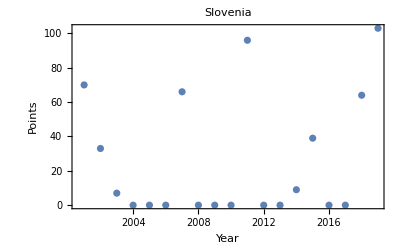

```mathematica
Graphfunction[2000, "Slovenia"]
```

And, if we don’t want to spend all the time searching for the year the country did best, we can use the function below. It will filter the data in accordance to the country, and the year from which we look onward, like in the previous cases.

```mathematica
TheBestYear[year_, country_]:=function[year, country]//Query[MaximalBy[Value[#Points]&]]
```

```mathematica
TheBestYear[2000, "Slovenia"]
```